## NaCs 1Σ Hamiltonian

## Setup

### Helper functions

```mathematica
kp[a_,b_]:=KroneckerProduct[a,b](*shorthand Kronecker product*)
conj=Complex[a_,b_]->Complex[a,-b];
Off[ClebschGordan::tri];
Off[ClebschGordan::phy];
J1dotJ2[J_,J1_,J2_]:=1/2(J(J+1)-J1(J1+1)-J2(J2+1))
```

### Constants and units

#### Definition

```mathematica
units=Association[cm->Quantity[1,"Centimeters"],um->Quantity[1,"Micrometers"],nm->Quantity[1,"Nanometers"],Hz->Quantity[1,"Hertz"],kHz->Quantity[1,"Kilohertz"],MHz->Quantity[1,"Megahertz"],GHz->Quantity[1,"Gigahertz"],THz->Quantity[1,"Terahertz"],icm->Quantity[1,("Centimeters")^-1],Debye->Quantity[1,"Debyes"],Gauss->Quantity[1,"Gauss"]];
fundamental=Association[ϵ0->Quantity["Permittivity of free space"],ℏ->Quantity["ReducedPlanckConstant"],h->Quantity["PlanckConstant"],μB->Quantity["BohrMagneton"],μN->Quantity["NuclearMagneton"],a0->Quantity[1,"BohrRadius"]];
nacs=Association[αpar->1872.12,αperp->467.038,Δ->αpar-αperp,α0->(αpar+2αperp)/3,Bv->h 1.7396 GHz,eQq1->-h 97 kHz,eQq2->h 150 kHz,c1->h 14.2 Hz,c2->h 854.5 Hz,c3->h 105.6 Hz,c4->h 3941.8 Hz,gr->0,g1->1.478,g2->0.738,σ1->0.0006392,σ2->0.0062787,d->4.6 Debye]/.units/.fundamental;
krb=Association[αpar->1872.12,αperp->467.038,Δ->αpar-αperp,α0->(αpar+2αperp)/3,Bv->h 1.11395 GHz,eQq1->h 450 kHz,eQq2->-h 1.41 MHz,c1->-h 24.1 Hz,c2->h 420.1 Hz,c3->h 0 Hz,c4->-h 2030.4 Hz,gr->0,g1->-0.324,g2->1.834,σ1->1321 10^-6,σ2->3469 10^-6,d->0 Debye]/.units/.fundamental;
experiment=Association[r->2.6 um,θh->(π-ArcCos[1/√3])/2,θq->π/2-ArcCos[1/√3],U->h 1 MHz,Bz->860 Gauss]/.units/.fundamental;
constants=Association[{units,fundamental,nacs,experiment}];
```

Quantity::conopen: Using Quantity requires internet connectivity. Please check your network connection. You may need to configure your firewall program or set a proxy in the Internet Connectivity tab of the Preferences dialog.

Quantity::unkunit: Unable to interpret unit specification Permittivity of free space.

### Hilbert space

```mathematica
{Nmin,Nmax}={0,1};
{I1,I2}={3/2,7/2};
nℋ=Sum[(2I1+1)(2I2+1)(2N+1),{N,Nmin,Nmax}];
ℋ=IdentityMatrix[nℋ];
sℋ=Partition[ℋ,{nℋ,1}][[1]];
```

### Basis

Basis labels

```mathematica
bUC={"I1","mI1","I2","mI2","N","mN"};
bSC={"I1","I2","I","mI","N","mN"};
bFC={"I1","I2","I","N","F","mF"};
bF1={"I1","I2","mI2","N","F1","mF1"};
bF2={"I1","mI1","I2","N","F2","mF2"};
```

Basis states

```mathematica
lUC=Flatten[Table[bUC/.{"I1"->I1,"mI1"->mI1,"I2"->I2,"mI2"->mI2,"N"->N,"mN"->mN},{mI1,-I1,I1},{mI2,-I2,I2},{N,Nmin,Nmax},{mN,-N,N}],3];
lSC=Flatten[Table[bSC/.{"I1"->I1,"I2"->I2,"I"->I,"mI"->mI,"N"->N,"mN"->mN},{I,Abs[I1-I2],I1+I2},{mI,-I,I},{N,Nmin,Nmax},{mN,-N,N}],3];
lFC=Flatten[Table[bFC/.{"I1"->I1,"I2"->I2,"I"->I,"N"->N,"F"->F,"mF"->mF},{I,Abs[I1-I2],I1+I2},{N,Nmin,Nmax},{F,Abs[I-N],I+N},{mF,-F,F}],3];
lF1=Flatten[Table[bF1/.{"I1"->I1,"I2"->I2,"mI2"->mI2,"N"->N,"F1"->F1,"mF1"->mF1},{mI2,-I2,I2},{N,Nmin,Nmax},{F1,Abs[I1-N],I1+N},{mF1,-F1,F1}],3];
lF2=Flatten[Table[bF2/.{"I1"->I1,"mI1"->mI1,"I2"->I2,"N"->N,"F2"->F2,"mF2"->mF2},{mI1,-I1,I1},{N,Nmin,Nmax},{F2,Abs[I2-N],I2+N},{mF2,-F2,F2}],3];
```

Check that the number of states matches the size of the Hilbert space for all bases.

```mathematica
(nℋ==Length[#])&/@{lUC,lSC,lFC,lF1,lF2}
```

{True,True,True,True,True}

Associate labels and states

```mathematica
b2l=AssociationThread[{bUC,bSC,bFC,bF1,bF2}->{lUC,lSC,lFC,lF1,lF2}];
```

Create basis transform matrix

```mathematica
b2b[bTo_,bFrom_,qTo_,qFrom_]:=With[{lTo=b2l[bTo],lFrom=b2l[bFrom],pFrom=Position[bFrom,#][[1,1]]&/@qFrom,pTo=Position[bTo,#][[1,1]]&/@qTo,pnTo=Position[bTo,#][[1,1]]&/@Intersection[bTo,bFrom],
pnFrom=Position[bFrom,#][[1,1]]&/@Intersection[bTo,bFrom]},Table[With[{to=lTo[[r]],from=lFrom[[c]]},If[to[[pnTo]]!=from[[pnFrom]],0,ClebschGordan[to[[pTo[[1;;2]]]],to[[pTo[[3;;4]]]],from[[pFrom]]]]],{r,Length[lTo]},{c,Length[lFrom]}]];
```

Basis transform matrices

```mathematica
SC2UC=b2b[bUC,bSC,{"I1","mI1","I2","mI2"},{"I","mI"}];
UC2SC=SC2UC†;
FC2SC=b2b[bSC,bFC,{"I","mI","N","mN"},{"F","mF"}];
SC2FC=FC2SC†;
F12UC=b2b[bUC,bF1,{"I1","mI1","N","mN"},{"F1","mF1"}];
UC2F1=F12UC†;
F22UC=b2b[bUC,bF2,{"I2","mI2","N","mN"},{"F2","mF2"}];
UC2F2=F22UC†;
F12FC=SC2FC.UC2SC.F12UC;
FC2F1=F12FC†;
F22FC=SC2FC.UC2SC.F22UC;
FC2F2=F22FC†;
UC2FC=SC2FC.UC2SC;
FC2UC=UC2FC†;
```

Check unitarity of basis transform matrix

```mathematica
UnitaryMatrixQ[#]&/@{SC2UC,FC2SC,F12UC,F22UC,F12FC,F22FC,UC2FC}
```

{True,True,True,True,True,True,True}

### Polarization

#### Jones vectors

```mathematica
qwp[θ_]=Exp[-(ⅈ π)/4]({{Cos[θ]^2+ⅈ Sin[θ]^2, (1-ⅈ) Sin[θ]Cos[θ]}, {(1-ⅈ) Sin[θ]Cos[θ], Sin[θ]^2+ⅈ Cos[θ]^2}});(*quarter waveplate Jones matrix*)
hwp[θ_]=Exp[-(ⅈ π)/2]({{Cos[θ]^2-Sin[θ]^2, 2Cos[θ]Sin[θ]}, {2Cos[θ]Sin[θ], Sin[θ]^2-Cos[θ]^2}});(*half waveplate Jones matrix*)
lpr[η_,θ_]=Exp[-(ⅈ η)/2]({{Cos[θ]^2+Exp[ⅈ η] Sin[θ]^2, (1-Exp[ⅈ η])Cos[θ]Sin[θ]}, {(1-Exp[ⅈ η])Cos[θ]Sin[θ], Sin[θ]^2+Exp[ⅈ η] Cos[θ]^2}});(*linear phase retarder Jones matrix*)

jH=({{1}, {0}});jV=({{0}, {1}});jL=1/(√2)({{1}, {ⅈ}});jR=1/(√2)({{1}, {-ⅈ}});(*Jones vectors for horizontal, vertical, LCP, and RCP light*)
jF[θh_,θq_]=FullSimplify[Flatten[hwp[θh].qwp[θq].jH],Assumptions->{0<=θh<2π,0<=θq<2π}];(*Jones vector seen by molecules*)
θd[θh_,θq_]:=ArcCos[Sin[2θh-θq]](*Angle between minor axis and array*)
```

```mathematica
pEllipse[θh_,θq_]=FullSimplify[ComplexExpand[Re[jF[θh,θq]Exp[-ⅈ t]]],Assumptions->{t>0,0<=θh<2π,0<=θq<2π}];
```

#### Polarizability

```mathematica
αMF=({{αperp, 0, 0}, {0, αperp, 0}, {0, 0, αpar}});(*Polarizability tensor in the molecular frame. It is diagonal for a linear molecule*)
Rx=RotationMatrix[θ,{1,0,0}];
Ry=RotationMatrix[θ,{0,1,0}];
Rz=RotationMatrix[ϕ,{0,0,1}];
αLF=Rzᵀ.Ryᵀ.αMF.Ry.Rz;
ϵ[θh_,θq_]={Append[jF[θh,θq],0]}ᵀ;(*Jones vector seen by the molecule, expressed in 3D coordinates*)
β[θ_,ϕ_]=-U/α0((ϵ[θh,θq]ᵀ/.Complex[a_,b_]->Complex[a,-b]).αLF.ϵ[θh,θq]-(αpar+2αperp)/3//FullSimplify)[[1,1]]/.(αpar-αperp)->Δ;(*Differential light shift relative to N=0. The rotation matrices express the polarizability tensor in the lab frame.*)
srAC[{n1_,m1_},{n2_,m2_}]:=(n1==n2∨Abs[n1-n2]==2)∧(m1==m2∨Abs[m1-m2]==2)(*Selection rules for coupling between states*)
meAC[{Np_,Nmp_},{N_,Nm_}]:=If[srAC[{Np,Nmp},{N,Nm}],Integrate[SphericalHarmonicY[Np,Nmp,θ,ϕ]*SphericalHarmonicY[N,Nm,θ,ϕ]β[θ,ϕ] Sin[θ],{θ,0,π},{ϕ,0,2π}],0]
bN={"N","mN"};
lN=Flatten[Table[bN/.{"N"->N,"mN"->mN},{N,Nmin,Nmax},{mN,-N,N}],1];
HacN=Table[meAC[lN[[i]],lN[[j]]],{i,1,Length[lN]},{j,1,Length[lN]}];
```

### DC electric field

```mathematica
srDC[{n1_,m1_},{n2_,m2_}]:=(n1==n2∨Abs[n1-n2]==2)∧(m1==m2∨Abs[m1-m2]==2)(*Selection rules for coupling between states*)
```

### Hamiltonian

#### Spin-spin scalar coupling (I_1·I_2)

```mathematica
HI1I2SC=With[{p=Position[bSC,#][[1,1]]&/@{"I","I1","I2"}},DiagonalMatrix[Table[With[{II1I2=lSC[[n,p]]},
J1dotJ2@@II1I2],{n,1,nℋ}]]];
HI1I2UC=SC2UC.HI1I2SC.UC2SC;
HermitianMatrixQ[HI1I2UC]
```

True

#### Spin-rotation scalar coupling (N·I_(1,2))

```mathematica
HNI1F1=With[{p=Position[bF1,#][[1,1]]&/@{"F1","N","I1"}},DiagonalMatrix[Table[With[{F1NI1=lF1[[n,p]]},
J1dotJ2@@F1NI1],{n,1,nℋ}]]];
HNI1UC=F12UC.HNI1F1.UC2F1;
HNI2F2=With[{p=Position[bF2,#][[1,1]]&/@{"F2","N","I2"}},DiagonalMatrix[Table[With[{F2NI2=lF2[[n,p]]},
J1dotJ2@@F2NI2],{n,1,nℋ}]]];
HNI2UC=F22UC.HNI2F2.UC2F2;
HermitianMatrixQ[#]&/@{HNI1UC,HNI2UC}
```

{True,True}

#### Electric quadrupole coupling

```mathematica
HEQ1F1=With[{p=Position[bF1,#][[1,1]]&/@{"F1","N","I1"}},DiagonalMatrix[Table[With[{F1=lF1[[n,p[[1]]]],N=lF1[[n,p[[2]]]],I1=lF1[[n,p[[3]]]]},
-(3 J1dotJ2[F1,N,I1]^2+3/2 J1dotJ2[F1,N,I1]-I1(I1+1)N(N+1))/(2I1(2I1-1)(2N-1)(2N+3))]
,{n,1,nℋ}]]];
HEQ2F2=With[{p=Position[bF2,#][[1,1]]&/@{"F2","N","I2"}},DiagonalMatrix[Table[With[{F2=lF2[[n,p[[1]]]],N=lF2[[n,p[[2]]]],I2=lF2[[n,p[[3]]]]},
-(3 J1dotJ2[F2,N,I2]^2+3/2 J1dotJ2[F2,N,I2]-I2(I2+1)N(N+1))/(2I2(2I2-1)(2N-1)(2N+3))]
,{n,1,nℋ}]]];
HEQ1UC=F12UC.HEQ1F1.UC2F1;
HEQ2UC=F22UC.HEQ2F2.UC2F2;
HermitianMatrixQ[#]&/@{HEQ1UC,HEQ2UC}
```

{True,True}

#### Zeeman coupling

```mathematica
HZNUC=With[{p=Position[bUC,"mN"][[1,1]]},DiagonalMatrix[Table[
lUC[[n,p]],{n,1,nℋ}]]];
HZI1UC=With[{p=Position[bUC,"mI1"][[1,1]]},DiagonalMatrix[Table[
lUC[[n,p]],{n,1,nℋ}]]];
HZI2UC=With[{p=Position[bUC,"mI2"][[1,1]]},DiagonalMatrix[Table[
lUC[[n,p]],{n,1,nℋ}]]];
HermitianMatrixQ[#]&/@{HZNUC,HZI1UC,HZI2UC}
```

{True,True,True}

#### Rotation

```mathematica
HNUC=With[{p=Position[bUC,"N"][[1,1]]},DiagonalMatrix[Table[
With[{N=lUC[[n,p]]},N(N+1)],{n,1,nℋ}]]];
```

#### Electric dipole

#### Light shifts

```mathematica
HacUC=With[{p=Position[bUC,#][[1,1]]&/@{"N","mN"},pn=Position[bUC,#][[1,1]]&/@{"mI1","mI2"}},ParallelTable[With[{to=Position[lN,lUC[[i,p]]][[1,1]],from=Position[lN,lUC[[j,p]]][[1,1]]},If[lUC[[i,pn]]==lUC[[j,pn]],HacN[[to,from]],0]],{i,1,nℋ},{j,1,nℋ}]];
```

#### Total Hamiltonian

```mathematica
HUC=Bv HNUC+c4 HI1I2UC+c1 HNI1UC+c2 HNI2UC+eQq1 HEQ1UC+eQq2 HEQ2UC-gr μN Bz HZNUC-g1 μN(1-σ1)Bz HZI1UC-g2 μN(1-σ2)Bz HZI2UC+HacUC;
```

## Evaluate Hamiltonian

### Total Hamiltonian with replacements

```mathematica
HUCn=HUC/h/.{U->h 10 MHz,Bz->860 Gauss}//.units//.constants//UnitConvert//QuantityMagnitude;
HFCn=UC2FC.HUCn.FC2UC;
HSCn=UC2SC.HUCn.SC2UC;
```

### Eigensystem of the Hamiltonian

```mathematica
eUC=Sort[Eigensystem[HUCn]ᵀ]ᵀ;
eSC=Sort[Eigensystem[HSCn]ᵀ]ᵀ;
eFC=Sort[Eigensystem[HFCn]ᵀ]ᵀ;
```

### Select eigenstates

```mathematica
s0s=Flatten[Position[lUC[[All,Flatten[{"mI1","mI2","N"}/.PositionIndex[bUC]]]],{3/2,5/2,0}]];
s1s=Flatten[Position[lUC[[All,Flatten[{"mI1","mI2","N"}/.PositionIndex[bUC]]]],{3/2,5/2,1}]];
s2s=Flatten[Position[lUC[[All,Flatten[{"mI1","mI2","N"}/.PositionIndex[bUC]]]],{3/2,5/2,2}]];
p0s=OrderingBy[eUC[[2,All,s0s]],Total[Abs[#]^2]&][[-1]];
p1s=OrderingBy[eUC[[2,All,s1s]],Total[Abs[#]^2]&][[-3;;-1]];
p2s=OrderingBy[eUC[[2,All,s2s]],Total[Abs[#]^2]&][[-5;;-1]];
```

### Decomposition of eigenstates

```mathematica
sUCp[n_,f_:0.1]:=Module[{sS,sP},sS=SortBy[Select[eUC[[2]][[n]],Abs[#]^2>=f&],Abs];
sP=Position[eUC[[2]][[n]],#][[1,1]]&/@sS;
Transpose@{Abs[#]^2&/@sS,lUC[[sP]]}]
sSCp[n_,f_:0.1]:=Module[{sS,sP},sS=SortBy[Select[eSC[[2]][[n]],Abs[#]^2>=f&],Abs];
sP=Position[eSC[[2]][[n]],#][[1,1]]&/@sS;
Transpose@{Abs[#]^2&/@sS,lUC[[sP]]}]
sFCp[n_,f_:0.1]:=Module[{sS,sP},sS=SortBy[Select[eFC[[2]][[n]],Abs[#]^2>=f&],Abs];
sP=Position[eFC[[2]][[n]],#][[1,1]]&/@sS;
Transpose@{Abs[#]^2&/@sS,lFC[[sP]]}]
```

```mathematica
sSCp[#,0.1]&/@{p0s}
```

{{{0.317388,{3/2,1/2,7/2,1/2,0,0}},{0.682612,{3/2,3/2,7/2,5/2,0,0}}}}

```mathematica
bSC
```

{I1,I2,I,mI,N,mN}

```mathematica
(eUC[[1,p2s]]-QuantityMagnitude[UnitConvert[6 Bv/h/.constants]])/10^6
```

{3.96837,-8.3567,-9.23757,3.07996,-2.64241}

```mathematica
bFC
```

{I1,I2,I,N,F,mF}

```mathematica
smF=Table[Round[Chop[(Abs[eFC[[2,i]]]^2).lFC][[-1]],0.5],{i,1,nℋ}];
pcl=ConstantArray[Black,nℋ];
pcl[[p0s]]=ColorData[3,2];
pcl[[p1s]]=ColorData[3,#]&/@{6,10,4};
```

```mathematica
pn0=Transpose@{smF[[1;;32]],10^-6 eFC[[1,1;;32]]};
pn1=Transpose@{smF[[33;;128]],(eFC[[1,33;;128]]-QuantityMagnitude[UnitConvert[2 Bv/h/.constants]])/10^6};
pn2=Transpose@{smF[[129;;nℋ]],(eFC[[1,129;;nℋ]]-QuantityMagnitude[UnitConvert[6 Bv/h/.constants]])/10^6};
```

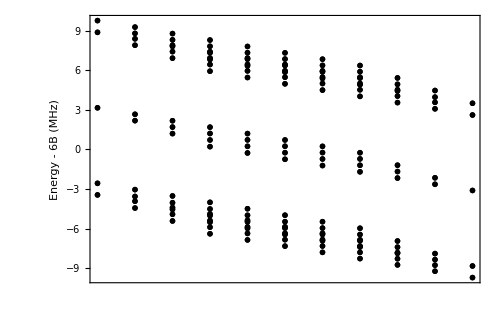

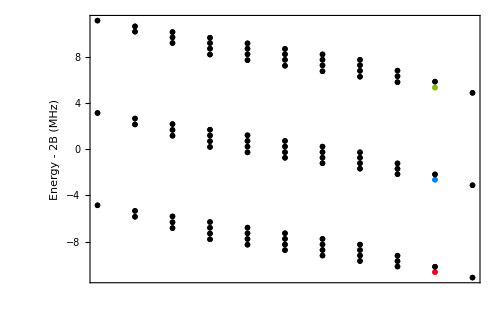

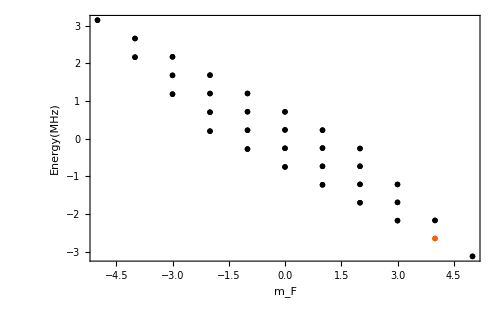

```mathematica
SetOptions[ListPlot,BaseStyle->{FontFamily->"Arial",FontSize->16},TicksStyle->Directive[Black,10],Frame->True,Joined->False,FrameTicks->{Automatic,Automatic},ImagePadding->{{60,10},{60,10}},ImageSize->500,AxesLabel->{"",""},PlotMarkers->{"—",25},PlotStyle->Black]; 
l2=ListPlot[{#}&/@pn2,FrameLabel->{"","Energy - 6B (MHz)"},PlotStyle->pcl[[129;;nℋ]],FrameTicks->{None,Automatic}]
l1=ListPlot[{#}&/@pn1,FrameLabel->{"","Energy - 2B (MHz)"},PlotStyle->pcl[[33;;128]],FrameTicks->{None,Automatic}]
l0=ListPlot[{#}&/@pn0,FrameLabel->{"m_F","Energy(MHz)"},PlotStyle->pcl[[1;;32]]]
```

```mathematica
yUC=lUC[[All,-2;;-1]]/.{n_,mn_}->SphericalHarmonicY[n,mn,θ,ϕ];
```

```mathematica
ep=Show[SphericalPlot3D[Abs[eUC[[2,p1s[[3]]]].yUC]^2,{θ,0,π},{ϕ,0,2π},PlotStyle->{ColorData[3,4],Opacity[0.3]},Mesh->False,Boxed->False,Axes->False,PlotPoints->20,PlotRange->All,ViewPoint->{-1,1,-2},ViewAngle->All,ViewVertical->{0, 1, 0}],ParametricPlot3D[Flatten[{pEllipse[π/4,0]/5,0}],{t,0,2π},ImageSize->Small,AxesLabel->{"x","y"},PlotStyle->{Black,Thickness[0.01]}],Graphics3D[{Thickness[0.01],Black,Arrow[{{0,0,0},{0,0,1/4}}],Thickness[0.005],Gray,Dashed,Line[{{-.3,0,0},{.3,0,0}}],Line[{{0,-.3,0},{0,.3,0}}],Text[Style["x",20,FontFamily->"Arial"],{0.33,0,0}],Text[Style["y",20,FontFamily->"Arial"],{0,.33,0}]}]]
e0=Show[SphericalPlot3D[Abs[eUC[[2,p1s[[1]]]].yUC]^2,{θ,0,π},{ϕ,0,2π},PlotStyle->{ColorData[3,6],Opacity[0.3]},Mesh->False,Boxed->False,Axes->False,PlotPoints->20,PlotRange->All,ViewPoint->{-1,1,-2},ViewAngle->All,ViewVertical->{0, 1, 0}],ParametricPlot3D[Flatten[{pEllipse[π/4,0]/5,0}],{t,0,2π},ImageSize->Small,AxesLabel->{"x","y"},PlotStyle->{Black,Thickness[0.01]}],Graphics3D[{Thickness[0.01],Black,Arrow[{{0,0,0},{0,0,1/4}}],Thickness[0.005],Gray,Dashed,Line[{{-.3,0,0},{.3,0,0}}],Line[{{0,-.3,0},{0,.3,0}}],Text[Style["x",20,FontFamily->"Arial"],{0.33,0,0}],Text[Style["y",20,FontFamily->"Arial"],{0,.33,0}]}]]
em=Show[SphericalPlot3D[Abs[eUC[[2,p1s[[2]]]].yUC]^2,{θ,0,π},{ϕ,0,2π},PlotStyle->{ColorData[3,10],Opacity[0.3]},Mesh->False,Boxed->False,Axes->False,PlotPoints->20,PlotRange->All,ViewPoint->{-1,1,-2},ViewAngle->All,ViewVertical->{0, 1, 0}],ParametricPlot3D[Flatten[{pEllipse[π/4,0]/5,0}],{t,0,2π},ImageSize->Small,AxesLabel->{"x","y"},PlotStyle->{Black,Thickness[0.01]}],Graphics3D[{Thickness[0.01],Black,Arrow[{{0,0,0},{0,0,1/4}}],Thickness[0.005],Gray,Dashed,Line[{{-.3,0,0},{.3,0,0}}],Line[{{0,-.3,0},{0,.3,0}}],Text[Style["x",20,FontFamily->"Arial"],{0.33,0,0}],Text[Style["y",20,FontFamily->"Arial"],{0,.33,0}]}]]
e00=Show[SphericalPlot3D[Abs[eUC[[2,p0s]].yUC]^2,{θ,0,π},{ϕ,0,2π},PlotStyle->{ColorData[3,2],Opacity[0.3]},Mesh->False,Boxed->False,Axes->False,PlotPoints->20,PlotRange->All,ViewPoint->{-1,1,-2},ViewAngle->All,ViewVertical->{0, 1, 0}],ParametricPlot3D[Flatten[{pEllipse[θh/.constants,θq/.constants]/5,0}],{t,0,2π},ImageSize->Small,AxesLabel->{"x","y"},PlotStyle->{Black,Thickness[0.01]}],Graphics3D[{Thickness[0.01],Black,Arrow[{{0,0,0},{0,0,1/4}}],Thickness[0.005],Gray,Dashed,Line[{{-.3,0,0},{.3,0,0}}],Line[{{0,-.3,0},{0,.3,0}}],Text[Style["x",20,FontFamily->"Arial"],{0.33,0,0}],Text[Style["y",20,FontFamily->"Arial"],{0,.33,0}]}]]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
Export["/Users/gpatenotte/Documents/Research/Ni Group/cuaRetreatPoster/e00.pdf",e00,"PDF"]
```

/Users/gpatenotte/Documents/Research/Ni Group/cuaRetreatPoster/e00.pdf

```mathematica
pEllipse[θh/.constants,θq/.constants]/.t->(3π)/4//FullSimplify
```

{1/(√3),0}

```mathematica
QuantityMagnitude[UnitConvert[2 Bv/h/.constants]]
```

3.4792×10^9

## End

```mathematica
bUC
```

{I1,mI1,I2,mI2,N,mN}

```mathematica
sUCy[s_]:=Module[{sAng},sAng=eUC[[2,s]].(lUC[[All,Flatten[{"N","mN"}/.PositionIndex[bUC]]]]/.{{n_,nM_}->SphericalHarmonicY[n,nM,θ,ϕ]});
SphericalPlot3D[Abs[sAng]^2,{θ,0,π},{ϕ,0,2π},PlotRange->All,AxesLabel->{"x","y","z"},ViewPoint->Front,ViewVertical->{0, 0, 1}]]
```

```mathematica
s0s=Flatten[Position[lUC[[All,Flatten[{"mI1","mI2","N"}/.PositionIndex[bUC]]]],{3/2,5/2,0}]];
s1s=Flatten[Position[lUC[[All,Flatten[{"mI1","mI2","N"}/.PositionIndex[bUC]]]],{3/2,5/2,1}]];
```

```mathematica
bUC
p0s=OrderingBy[eUC[[2,All,s0s]],Total[Abs[#]^2]&][[-1]];
p1s=OrderingBy[eUC[[2,All,s1s]],Total[Abs[#]^2]&][[-3;;-1]];
sUCp[p0s]
sUCp[#]&/@p1s
```

{I1,mI1,I2,mI2,N,mN}

{{0.49896,{3/2,-1/2,7/2,3/2,1,-1}},{0.499312,{3/2,-1/2,7/2,3/2,1,1}}}

{{{0.498922,{3/2,-1/2,7/2,3/2,2,1}},{0.49939,{3/2,-1/2,7/2,3/2,2,-1}}},{{0.463094,{3/2,-1/2,7/2,3/2,2,2}},{0.468538,{3/2,-1/2,7/2,3/2,2,-2}}},{{0.930986,{3/2,-1/2,7/2,3/2,2,0}}}}

```mathematica
p1s
```

{208,153,260}

```mathematica
eFC[[2,2]].lFC
```

{-2.08436,-4.86351,-6.3845,-2.75408×10^-16,-6.3845,-5.5583}

```mathematica
Round[Chop[(Abs[eFC[[2,34]]]^2).lFC],0.5]
```

{1.5,3.5,4.5,1.,5.,4.}

```mathematica
sFCp[2]
```

{{0.317388,{3/2,7/2,4,0,4,4}},{0.682612,{3/2,7/2,5,0,5,4}}}

```mathematica
Chop[(Abs[eUC[[2,37]]]^2).lUC]
```

{1.5,0.500908,3.5,3.49948,1.,-0.0112022}

```mathematica
p1s
```

{39,34,40}

```mathematica
bUC
```

{I1,mI1,I2,mI2,N,mN}

```mathematica
Sort[Transpose@{eUC[[1,#]]-QuantityMagnitude[UnitConvert[2 Bv/h/.constants]]-eUC[[1,p0s]],sUCy[#]}&/@p1s]
```

{{-397517.,-Graphics3D-},{193034.,-Graphics3D-},{203648.,-Graphics3D-}}

```mathematica
bUC
sUCp[p1s[[2]],0.0001]
```

{I1,mI1,I2,mI2,N,mN}

{{0.000205223,{3/2,1/2,7/2,7/2,1,-1}},{0.000218574,{3/2,1/2,7/2,7/2,1,1}},{0.00341965,{3/2,3/2,7/2,7/2,1,0}},{0.494668,{3/2,3/2,7/2,5/2,1,1}},{0.501278,{3/2,3/2,7/2,5/2,1,-1}}}

```mathematica
eUC[[1,p1s]]-3.476564688 10^9
```

{188665.,-401886.,199279.}

```mathematica
eUC[[1,p1s[[1]]]]
```

3.47675×10^9

```mathematica
s1s
```

{122,123,124}

```mathematica
eUC[[2,p1s[[1]]]][[s1s]]
```

{-9.59906×10^-12,0.997591,-1.0587×10^-11}

```mathematica
lUC[[s1s]]
```

{{3/2,3/2,7/2,5/2,1,-1},{3/2,3/2,7/2,5/2,1,0},{3/2,3/2,7/2,5/2,1,1}}

# Stop

```mathematica
energyPerDepth[depth_]:=Module[{HUCn0,eUC0,p1s0},HUCn0=HUC/h/.krb/.U->h  depth MHz//.constants//UnitConvert//QuantityMagnitude;
eUC0=Sort[Eigensystem[HUCn0]ᵀ]ᵀ;
p1s0=OrderingBy[eUC0[[2,All,s1s]],Total[Abs[#]^2]&][[-3;;-1]];
{eUC0[[1]],p1s0}]
energyPerMag[b_]:=Module[{HUCn0,eUC0,p1s0,p0s0},HUCn0=HUC/h/.Bz->b Gauss/.U->h  10 MHz//.constants//UnitConvert//QuantityMagnitude;
eUC0=Sort[Eigensystem[HUCn0]ᵀ]ᵀ;
p0s0=OrderingBy[eUC0[[2,All,s0s]],Total[Abs[#]^2]&][[-1]];
p1s0=OrderingBy[eUC0[[2,All,s1s]],Total[Abs[#]^2]&][[-3;;-1]];
eUC0[[1,#]]&/@Flatten[{p0s0,p1s0}]]
energyPerAngle[a_]:=Module[{HUCn0,eUC0,p1s0},HUCn0=HUC/h/.θq->a/.U->h  1 MHz//.constants//UnitConvert//QuantityMagnitude;
eUC0=Sort[Eigensystem[HUCn0]ᵀ]ᵀ;
p1s0=OrderingBy[eUC0[[2,All,s1s]],Total[Abs[#]^2]&][[-3;;-1]];
eUC0[[1,#]]&/@p1s0]
```

```mathematica
ds=Range[0.001,.5,0.01];
bs=Range[859,861,.1];
as=θq/.constants+π/180 Range[-.1,.1,.01]
```

{0.613734,0.613909,0.614083,0.614258,0.614433,0.614607,0.614782,0.614956,0.615131,0.615305,0.61548,0.615654,0.615829,0.616003,0.616178,0.616352,0.616527,0.616701,0.616876,0.617051,0.617225}

```mathematica
epaTab=ParallelTable[energyPerAngle[a],{a,as}];
```

```mathematica
epbTab=ParallelTable[energyPerMag[b],{b,bs}];
```

```mathematica
epbTab[[All,1]]//Length
```

9

```mathematica
((Sort/@epbTab)ᵀ[[#]]&/@{2})[[1]]//Length
```

9

```mathematica
{5,4}-{3,2}
```

{2,2}

```mathematica
(Sort/@epbTab)ᵀ[[3]]-epbTab[[All,1]]-3.479223432768477*^9
```

{1.96315×10^6+0. ⅈ,-21246.4+0. ⅈ,-20227.5+0. ⅈ,-19993.8+0. ⅈ,-19884.8+0. ⅈ,-19813.+0. ⅈ,-19880.4+0. ⅈ,-19672.6+0. ⅈ,-19500.8+0. ⅈ}

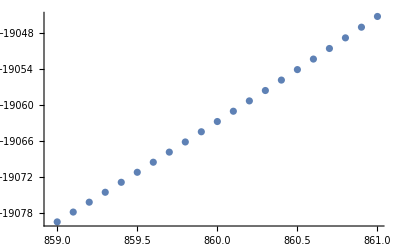

```mathematica
ListPlot[Transpose@{bs,(Sort/@epbTab)ᵀ[[3]]-epbTab[[All,1]]-3.479223432768477*^9},PlotRange->All]
```

```mathematica
35/2
```

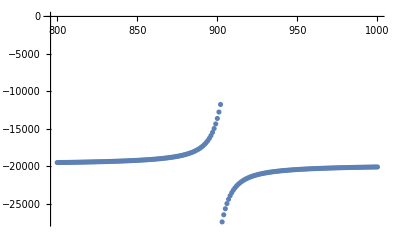

-Graphics-

```mathematica
test=(Sort/@epaTab)ᵀ[[#]]-3.4765639516*^9&/@{2}
(test[[1,1]]-test[[1,-1]])/2
```

{{986.518,887.922,789.315,690.695,592.064,493.42,394.764,296.095,197.415,98.7227,0.0182252+0. ⅈ,-98.6983,-197.427,-296.168,-394.92,-493.685,-592.461,-691.25,-790.051,-888.863,-987.688}}

987.103

```mathematica
987/1
```

987

```mathematica
8.6/8.7//N
```

0.988506

```mathematica
-1.51673+25.5749x/.x->2
```

49.6331

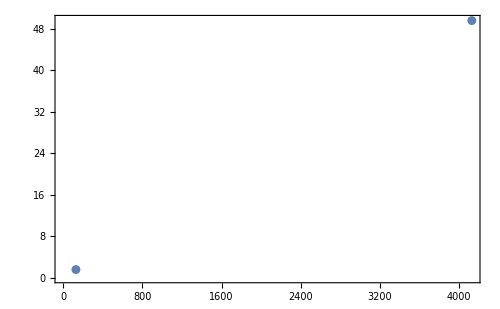

1.54991+0.673768 x

```mathematica
ListPlot[{{(71.356-71.35587104825288)10^6,1.55},{(71.36-71.35587104825288)10^6,49.63}}]
fit=Fit[{{71.356-71.35587104825288,1.55},{71.36,49.63}},{1,x},x]
```

```mathematica
(4 10^3)/49.63
```

80.5964

```mathematica
71.356-71.35587104825288
```

0.000128952

```mathematica
Solve[-857697.5699978296+12019.999999969588 x==0,x]
```

{{x→71.3559}}

```mathematica
15 10
```

```mathematica
epbTab[[-1]]-epbTab[[1]]
```

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
epdTab=ParallelTable[energyPerDepth[d],{d,ds}];
```

{{2.22526×10^9+0. ⅈ,2.22526×10^9+0. ⅈ,2.22526×10^9+0. ⅈ,2.22526×10^9+0. ⅈ,2.22527×10^9+0. ⅈ,2.22527×10^9+0. ⅈ,2.22527×10^9+0. ⅈ,2.22527×10^9+0. ⅈ,2.22527×10^9+0. ⅈ,2.22527×10^9+0. ⅈ,2.22528×10^9+0. ⅈ,2.22528×10^9+0. ⅈ,2.22528×10^9+0. ⅈ,2.22528×10^9+0. ⅈ,2.22528×10^9+0. ⅈ,2.22529×10^9+0. ⅈ,2.22529×10^9+0. ⅈ,2.22529×10^9+0. ⅈ,2.22518×10^9+0. ⅈ,2.22518×10^9+0. ⅈ,2.22518×10^9+0. ⅈ,2.22518×10^9+0. ⅈ,2.22517×10^9+0. ⅈ,2.22517×10^9+0. ⅈ,2.22517×10^9+0. ⅈ,2.22517×10^9+0. ⅈ,2.22517×10^9+0. ⅈ,2.22516×10^9+0. ⅈ,2.22516×10^9+0. ⅈ,2.22516×10^9+0. ⅈ,2.22516×10^9+0. ⅈ,2.22516×10^9+0. ⅈ,2.22516×10^9+0. ⅈ,2.22515×10^9+0. ⅈ,2.22515×10^9+0. ⅈ,2.22515×10^9+0. ⅈ,2.22515×10^9+0. ⅈ,2.22515×10^9+0. ⅈ,2.22515×10^9+0. ⅈ,2.22514×10^9+0. ⅈ,2.22514×10^9+0. ⅈ,2.22514×10^9+0. ⅈ,2.22514×10^9+0. ⅈ,2.22514×10^9+0. ⅈ,2.22514×10^9+0. ⅈ,2.22513×10^9+0. ⅈ,2.22513×10^9+0. ⅈ,2.22513×10^9+0. ⅈ,2.22513×10^9+0. ⅈ,2.22513×10^9+0. ⅈ},{2.22521×10^9+0. ⅈ,2.22521×10^9+0. ⅈ,2.22521×10^9+0. ⅈ,2.22521×10^9+0. ⅈ,2.22521×10^9+0. ⅈ,2.22521×10^9+0. ⅈ,2.22521×10^9+0. ⅈ,2.22521×10^9+0. ⅈ,2.22521×10^9+0. ⅈ,2.22521×10^9+0. ⅈ,2.22521×10^9+0. ⅈ,2.22519×10^9+0. ⅈ,2.22519×10^9+0. ⅈ,2.22519×10^9+0. ⅈ,2.22519×10^9+0. ⅈ,2.22519×10^9+0. ⅈ,2.22518×10^9+0. ⅈ,2.22518×10^9+0. ⅈ,2.22529×10^9+0. ⅈ,2.22529×10^9+0. ⅈ,2.22529×10^9+0. ⅈ,2.2253×10^9+0. ⅈ,2.2253×10^9+0. ⅈ,2.22521×10^9+0. ⅈ,2.22521×10^9+0. ⅈ,2.22522×10^9+0. ⅈ,2.22522×10^9+0. ⅈ,2.22522×10^9+0. ⅈ,2.22522×10^9+0. ⅈ,2.22522×10^9+0. ⅈ,2.22522×10^9+0. ⅈ,2.22522×10^9+0. ⅈ,2.22522×10^9+0. ⅈ,2.22522×10^9+0. ⅈ,2.22522×10^9+0. ⅈ,2.22522×10^9+0. ⅈ,2.22522×10^9+0. ⅈ,2.22522×10^9+0. ⅈ,2.22522×10^9+0. ⅈ,2.22522×10^9+0. ⅈ,2.22522×10^9+0. ⅈ,2.22522×10^9+0. ⅈ,2.22522×10^9+0. ⅈ,2.22522×10^9+0. ⅈ,2.22522×10^9+0. ⅈ,2.22522×10^9+0. ⅈ,2.22522×10^9+0. ⅈ,2.22522×10^9+0. ⅈ,2.22522×10^9+0. ⅈ,2.22522×10^9+0. ⅈ},{2.22521×10^9+0. ⅈ,2.22521×10^9+0. ⅈ,2.22521×10^9+0. ⅈ,2.22521×10^9+0. ⅈ,2.22521×10^9+0. ⅈ,2.2252×10^9+0. ⅈ,2.2252×10^9+0. ⅈ,2.2252×10^9+0. ⅈ,2.2252×10^9+0. ⅈ,2.2252×10^9+0. ⅈ,2.2252×10^9+0. ⅈ,2.22521×10^9+0. ⅈ,2.22521×10^9+0. ⅈ,2.22521×10^9+0. ⅈ,2.22521×10^9+0. ⅈ,2.22521×10^9+0. ⅈ,2.22521×10^9+0. ⅈ,2.22521×10^9+0. ⅈ,2.22521×10^9+0. ⅈ,2.22521×10^9+0. ⅈ,2.22521×10^9+0. ⅈ,2.22521×10^9+0. ⅈ,2.22521×10^9+0. ⅈ,2.2253×10^9+0. ⅈ,2.2253×10^9+0. ⅈ,2.2253×10^9+0. ⅈ,2.22531×10^9+0. ⅈ,2.22531×10^9+0. ⅈ,2.22531×10^9+0. ⅈ,2.22531×10^9+0. ⅈ,2.22531×10^9+0. ⅈ,2.22531×10^9+0. ⅈ,2.22532×10^9+0. ⅈ,2.22532×10^9+0. ⅈ,2.22532×10^9+0. ⅈ,2.22532×10^9+0. ⅈ,2.22532×10^9+0. ⅈ,2.22533×10^9+0. ⅈ,2.22533×10^9+0. ⅈ,2.22533×10^9+0. ⅈ,2.22533×10^9+0. ⅈ,2.22533×10^9+0. ⅈ,2.22534×10^9+0. ⅈ,2.22534×10^9+0. ⅈ,2.22534×10^9+0. ⅈ,2.22534×10^9+0. ⅈ,2.22534×10^9+0. ⅈ,2.22534×10^9+0. ⅈ,2.22535×10^9+0. ⅈ,2.22535×10^9+0. ⅈ}}

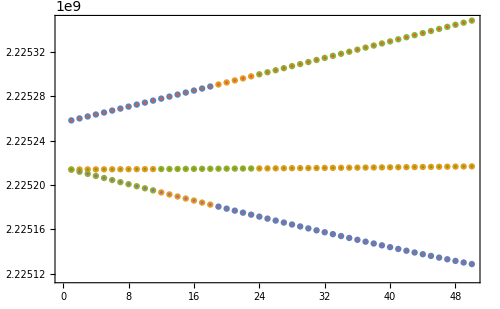

```mathematica
Show[ListPlot[Table[epdTab[[i,1]][[epdTab[[i,2]]]],{i,1,50}]ᵀ],ListPlot[epdTab[[All,1]]ᵀ]]
```

```mathematica
SetOptions[ListPlot,BaseStyle->{FontFamily->"Arial",FontSize->16},TicksStyle->Directive[Black,10],Frame->True,Joined->False,FrameTicks->{Automatic,Automatic},ImagePadding->{{60,10},{60,10}},ImageSize->500];
```

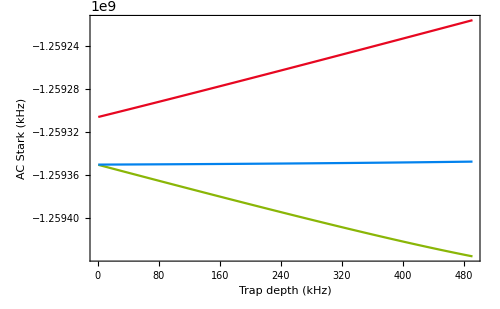

```mathematica
ListPlot[Transpose@{ds 10^3,(Sort/@epdTab)ᵀ[[#]]-(eUC[[1,p1s[[3]]]])}&/@{1,2,3},Joined->True,PlotStyle->(ColorData[3,#]&/@{4,6,10}),FrameLabel->{"Trap depth (kHz)","AC Stark (kHz)"}]
```

```mathematica
HUCn=HUC/h/.U->h  0 MHz//.constants//UnitConvert//QuantityMagnitude;
eUC=Sort[Eigensystem[HUCn]ᵀ]ᵀ;
p0s=OrderingBy[eUC[[2,All,s0s]],Total[Abs[#]^2]&][[-1]];
p1s=OrderingBy[eUC[[2,All,s1s]],Total[Abs[#]^2]&][[-3;;-1]];
```

```mathematica
eUC[[1,p0s]]
```

-3.114351541395[[1,p0s]]

```mathematica
eUC[[1,p1s[[2]]]]-eUC[[1,p0s]]
```

3.47919×10^9

```mathematica
(Sort/@epdTab)ᵀ
```

{{3.47655×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47655×10^9+0. ⅈ,3.47655×10^9+0. ⅈ,3.47655×10^9+0. ⅈ,3.47655×10^9+0. ⅈ,3.47655×10^9+0. ⅈ,3.47655×10^9+0. ⅈ,3.47654×10^9+0. ⅈ,3.47654×10^9+0. ⅈ,3.47654×10^9+0. ⅈ,3.47654×10^9+0. ⅈ,3.47654×10^9+0. ⅈ,3.47653×10^9+0. ⅈ,3.47653×10^9+0. ⅈ,3.47653×10^9+0. ⅈ,3.47653×10^9+0. ⅈ,3.47653×10^9+0. ⅈ,3.47652×10^9+0. ⅈ,3.47652×10^9+0. ⅈ,3.47652×10^9+0. ⅈ,3.47652×10^9+0. ⅈ,3.47652×10^9+0. ⅈ,3.47651×10^9+0. ⅈ,3.47651×10^9+0. ⅈ,3.47651×10^9+0. ⅈ,3.47651×10^9+0. ⅈ,3.47651×10^9+0. ⅈ,3.4765×10^9+0. ⅈ,3.4765×10^9+0. ⅈ,3.4765×10^9+0. ⅈ,3.4765×10^9+0. ⅈ,3.4765×10^9+0. ⅈ,3.47649×10^9+0. ⅈ,3.47649×10^9+0. ⅈ,3.47649×10^9+0. ⅈ,3.47649×10^9+0. ⅈ,3.47649×10^9+0. ⅈ,3.47648×10^9+0. ⅈ,3.47648×10^9+0. ⅈ,3.47648×10^9+0. ⅈ,3.47648×10^9+0. ⅈ,3.47648×10^9+0. ⅈ,3.47647×10^9+0. ⅈ,3.47647×10^9+0. ⅈ,3.47647×10^9+0. ⅈ,3.47647×10^9+0. ⅈ,3.47647×10^9+0. ⅈ,3.47646×10^9+0. ⅈ,3.47646×10^9+0. ⅈ,3.47646×10^9+0. ⅈ,3.47646×10^9+0. ⅈ,3.47646×10^9+0. ⅈ,3.47645×10^9+0. ⅈ,3.47645×10^9+0. ⅈ,3.47645×10^9+0. ⅈ,3.47645×10^9+0. ⅈ,3.47645×10^9+0. ⅈ,3.47644×10^9+0. ⅈ,3.47644×10^9+0. ⅈ,3.47644×10^9+0. ⅈ,3.47644×10^9+0. ⅈ,3.47644×10^9+0. ⅈ,3.47643×10^9+0. ⅈ,3.47643×10^9+0. ⅈ,3.47643×10^9+0. ⅈ,3.47643×10^9+0. ⅈ,3.47643×10^9+0. ⅈ,3.47642×10^9+0. ⅈ,3.47642×10^9+0. ⅈ,3.47642×10^9+0. ⅈ,3.47642×10^9+0. ⅈ,3.47642×10^9+0. ⅈ,3.47641×10^9+0. ⅈ,3.47641×10^9+0. ⅈ,3.47641×10^9+0. ⅈ,3.47641×10^9+0. ⅈ,3.47641×10^9+0. ⅈ,3.4764×10^9+0. ⅈ,3.4764×10^9+0. ⅈ,3.4764×10^9+0. ⅈ,3.4764×10^9+0. ⅈ,3.4764×10^9+0. ⅈ,3.47639×10^9+0. ⅈ,3.47639×10^9+0. ⅈ,3.47639×10^9+0. ⅈ,3.47639×10^9+0. ⅈ,3.47639×10^9+0. ⅈ,3.47638×10^9+0. ⅈ,3.47638×10^9+0. ⅈ,3.47638×10^9+0. ⅈ,3.47638×10^9+0. ⅈ,3.47638×10^9+0. ⅈ,3.47637×10^9+0. ⅈ,3.47637×10^9+0. ⅈ,3.47637×10^9+0. ⅈ,3.47637×10^9+0. ⅈ,3.47637×10^9+0. ⅈ},{3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ},{3.47657×10^9+0. ⅈ,3.47657×10^9+0. ⅈ,3.47657×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47656×10^9+0. ⅈ,3.47657×10^9+0. ⅈ,3.47657×10^9+0. ⅈ,3.47657×10^9+0. ⅈ,3.47657×10^9+0. ⅈ,3.47657×10^9+0. ⅈ,3.47658×10^9+0. ⅈ,3.47658×10^9+0. ⅈ,3.47658×10^9+0. ⅈ,3.47658×10^9+0. ⅈ,3.47658×10^9+0. ⅈ,3.47659×10^9+0. ⅈ,3.47659×10^9+0. ⅈ,3.47659×10^9+0. ⅈ,3.47659×10^9+0. ⅈ,3.47659×10^9+0. ⅈ,3.4766×10^9+0. ⅈ,3.4766×10^9+0. ⅈ,3.4766×10^9+0. ⅈ,3.4766×10^9+0. ⅈ,3.4766×10^9+0. ⅈ,3.47661×10^9+0. ⅈ,3.47661×10^9+0. ⅈ,3.47661×10^9+0. ⅈ,3.47661×10^9+0. ⅈ,3.47661×10^9+0. ⅈ,3.47662×10^9+0. ⅈ,3.47662×10^9+0. ⅈ,3.47662×10^9+0. ⅈ,3.47662×10^9+0. ⅈ,3.47662×10^9+0. ⅈ,3.47663×10^9+0. ⅈ,3.47663×10^9+0. ⅈ,3.47663×10^9+0. ⅈ,3.47663×10^9+0. ⅈ,3.47663×10^9+0. ⅈ,3.47664×10^9+0. ⅈ,3.47664×10^9+0. ⅈ,3.47664×10^9+0. ⅈ,3.47664×10^9+0. ⅈ,3.47664×10^9+0. ⅈ,3.47665×10^9+0. ⅈ,3.47665×10^9+0. ⅈ,3.47665×10^9+0. ⅈ,3.47665×10^9+0. ⅈ,3.47665×10^9+0. ⅈ,3.47666×10^9+0. ⅈ,3.47666×10^9+0. ⅈ,3.47666×10^9+0. ⅈ,3.47666×10^9+0. ⅈ,3.47666×10^9+0. ⅈ,3.47667×10^9+0. ⅈ,3.47667×10^9+0. ⅈ,3.47667×10^9+0. ⅈ,3.47667×10^9+0. ⅈ,3.47667×10^9+0. ⅈ,3.47667×10^9+0. ⅈ,3.47668×10^9+0. ⅈ,3.47668×10^9+0. ⅈ,3.47668×10^9+0. ⅈ,3.47668×10^9+0. ⅈ,3.47668×10^9+0. ⅈ,3.47669×10^9+0. ⅈ,3.47669×10^9+0. ⅈ,3.47669×10^9+0. ⅈ,3.47669×10^9+0. ⅈ,3.47669×10^9+0. ⅈ,3.4767×10^9+0. ⅈ,3.4767×10^9+0. ⅈ,3.4767×10^9+0. ⅈ,3.4767×10^9+0. ⅈ,3.4767×10^9+0. ⅈ,3.47671×10^9+0. ⅈ,3.47671×10^9+0. ⅈ,3.47671×10^9+0. ⅈ,3.47671×10^9+0. ⅈ,3.47671×10^9+0. ⅈ,3.47672×10^9+0. ⅈ,3.47672×10^9+0. ⅈ,3.47672×10^9+0. ⅈ,3.47672×10^9+0. ⅈ,3.47672×10^9+0. ⅈ,3.47673×10^9+0. ⅈ,3.47673×10^9+0. ⅈ,3.47673×10^9+0. ⅈ,3.47673×10^9+0. ⅈ,3.47673×10^9+0. ⅈ,3.47674×10^9+0. ⅈ,3.47674×10^9+0. ⅈ,3.47674×10^9+0. ⅈ,3.47674×10^9+0. ⅈ,3.47674×10^9+0. ⅈ,3.47675×10^9+0. ⅈ,3.47675×10^9+0. ⅈ,3.47675×10^9+0. ⅈ}}

```mathematica
pn0
```

{{5.,-3.1246},{4.,-2.64993},{3.,-2.17521},{4.,-2.16995},{2.,-1.70044},{3.,-1.69128},{1.,-1.22562},{3.,-1.21542},{2.,-1.21259},{0.,-0.75075},{1.,-0.733879},{2.,-0.732706},{-1.,-0.275837},{2.,-0.260996},{0.,-0.255151},{1.,-0.25001},{-2.,0.199121},{-1.,0.223594},{1.,0.225791},{0.,0.232672},{-2.,0.702356},{0.,0.712527},{-1.,0.715339},{-3.,1.18114},{-2.,1.19799},{-1.,1.19921},{-3.,1.68063},{-2.,1.68585},{-4.,2.16326},{-3.,2.17244},{-4.,2.65899},{-5.,3.14549}}

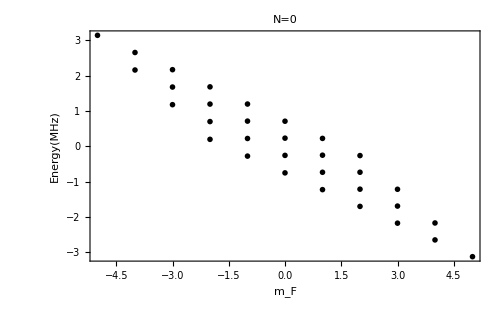

```mathematica
ListPlot[Evaluate[pn0],PlotLabel->"N=0",FrameLabel->{"m_F","Energy(MHz)"},PlotStyle->pcl]
```

```mathematica
pn0
```

{{5.,-3.1246},{4.,-2.64993},{3.,-2.17521},{4.,-2.16995},{2.,-1.70044},{3.,-1.69128},{1.,-1.22562},{3.,-1.21542},{2.,-1.21259},{0.,-0.75075},{1.,-0.733879},{2.,-0.732706},{-1.,-0.275837},{2.,-0.260996},{0.,-0.255151},{1.,-0.25001},{-2.,0.199121},{-1.,0.223594},{1.,0.225791},{0.,0.232672},{-2.,0.702356},{0.,0.712527},{-1.,0.715339},{-3.,1.18114},{-2.,1.19799},{-1.,1.19921},{-3.,1.68063},{-2.,1.68585},{-4.,2.16326},{-3.,2.17244},{-4.,2.65899},{-5.,3.14549}}

```mathematica
pn0//Length
```

32

```mathematica
pcl=Join[{Black,ColorData[3,2]},ConstantArray[Black,30]]
```

{GrayLevel[0],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0]}

```mathematica
Export["/Users/gpatenotte/Documents/Research/Ni Group/cuaRetreatPoster/elp.pdf",ep,"PDF"]
```

/Users/gpatenotte/Documents/Research/Ni Group/cuaRetreatPoster/elp.pdf

```mathematica
SetOptions[ListPlot,BaseStyle->{FontFamily->"Arial",FontSize->16},TicksStyle->Directive[Black,10],Frame->True,Joined->False,FrameTicks->{Automatic,Automatic},ImagePadding->{{60,10},{60,10}},ImageSize->500,AxesLabel->{"",""},PlotMarkers->{"—",25},PlotStyle->Black]; 
l2=ListPlot[{#}&/@pn2,FrameLabel->{"","Energy - 6B (MHz)"},PlotStyle->pcl[[129;;nℋ]],FrameTicks->{None,Automatic}]
l1=ListPlot[{#}&/@pn1,FrameLabel->{"","Energy - 2B (MHz)"},PlotStyle->pcl[[33;;128]],FrameTicks->{None,Automatic}]
l0=ListPlot[{#}&/@pn0,FrameLabel->{"m_F","Energy(MHz)"},PlotStyle->pcl[[1;;32]]]
```

```mathematica
ListPlot[{}]
```

-Graphics-

```mathematica
pn2
```

{{5.,-9.7202},{4.,-9.23757},{5.,-8.84051},{4.,-8.77755},{3.,-8.75752},{4.,-8.3567},{3.,-8.29091},{2.,-8.28006},{4.,-7.89971},{3.,-7.87588},{3.,-7.823},{2.,-7.80689},{1.,-7.80522},{3.,-7.41189},{2.,-7.39805},{0.,-7.333},{2.,-7.33232},{1.,-7.32549},{3.,-6.94517},{2.,-6.9271},{1.,-6.92322},{-1.,-6.86341},{2.,-6.85658},{0.,-6.84675},{1.,-6.84429},{2.,-6.45331},{0.,-6.4514},{1.,-6.44533},{-2.,-6.39645},{-1.,-6.37066},{1.,-6.36183},{0.,-6.35893},{-1.,-5.98258},{2.,-5.9769},{0.,-5.96659},{1.,-5.96451},{-2.,-5.89723},{-1.,-5.87624},{0.,-5.86977},{-2.,-5.51678},{-1.,-5.49089},{1.,-5.48097},{0.,-5.47877},{-3.,-5.42645},{-2.,-5.39625},{-1.,-5.3804},{-2.,-5.01823},{-1.,-4.99609},{0.,-4.98813},{-3.,-4.91894},{-2.,-4.89375},{-3.,-4.54862},{-2.,-4.51649},{-1.,-4.49839},{-4.,-4.44431},{-3.,-4.40981},{-3.,-4.03995},{-2.,-4.01174},{-4.,-3.92859},{-4.,-3.56648},{-3.,-3.5282},{-5.,-3.45007},{5.,-3.11249},{-4.,-3.04775},{4.,-2.64241},{-5.,-2.5704},{3.,-2.17075},{4.,-2.15092},{2.,-1.6975},{3.,-1.67685},{1.,-1.22266},{2.,-1.20122},{3.,-1.19635},{0.,-0.746247},{1.,-0.724028},{2.,-0.718236},{-1.,-0.268267},{2.,-0.248855},{0.,-0.245281},{1.,-0.238602},{-2.,0.211256},{1.,0.233335},{-1.,0.235015},{0.,0.242558},{-2.,0.716846},{0.,0.717011},{-1.,0.725245},{-3.,1.20019},{-1.,1.20218},{-2.,1.20945},{-2.,1.68884},{-3.,1.69516},{-3.,2.17698},{-4.,2.18235},{5.,2.60989},{-4.,2.66659},{4.,3.07996},{-5.,3.15765},{5.,3.50163},{3.,3.55163},{4.,3.57151},{4.,3.96837},{2.,4.02487},{3.,4.04558},{3.,4.43781},{4.,4.46833},{1.,4.4997},{2.,4.52121},{3.,4.52603},{2.,4.90995},{3.,4.93906},{0.,4.9761},{1.,4.99839},{2.,5.00414},{1.,5.38479},{2.,5.41246},{3.,5.42282},{-1.,5.45407},{2.,5.47359},{0.,5.47712},{1.,5.48377},{0.,5.86231},{1.,5.88853},{2.,5.89759},{-2.,5.93361},{1.,5.95577},{-1.,5.9574},{0.,5.96493},{-1.,6.34251},{2.,6.36529},{0.,6.36728},{1.,6.375},{-2.,6.43922},{0.,6.43944},{-1.,6.44761},{-2.,6.82538},{1.,6.84414},{-1.,6.84868},{0.,6.85505},{-3.,6.92258},{-1.,6.9246},{-2.,6.9318},{0.,7.3256},{-2.,7.33274},{-1.,7.33774},{-2.,7.41125},{-3.,7.4175},{-1.,7.80965},{-3.,7.81943},{-2.,7.82305},{-3.,7.89937},{-4.,7.9047},{-2.,8.29631},{-3.,8.31098},{-4.,8.38898},{-3.,8.78556},{-4.,8.80151},{-5.,8.88005},{-4.,9.27739},{-5.,9.77179}}

```mathematica
p1s-32
```

{34,2,66}

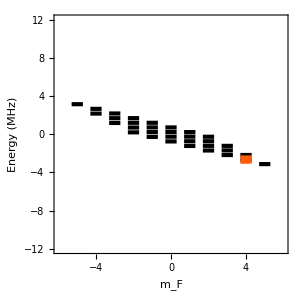

```mathematica
SetOptions[ListPlot,BaseStyle->{FontFamily->"Arial",FontSize->16},TicksStyle->Directive[Black,10],Frame->True,Joined->False,FrameTicks->{Automatic,Automatic},ImagePadding->{{60,10},{60,10}},ImageSize->300,AxesLabel->{"",""},PlotMarkers->{"—",25},PlotStyle->Black]; 
ml[{x_,y_},color_:Black]:={color,Line[{{x-0.3,y},{x+0.3,y}}]}
l0=Show[ListPlot[{},FrameLabel->{"m_F","Energy (MHz)"},PlotRange->{{-6,6},{-12,12}}],Graphics[{ml/@pn0,Thickness[0.02],ml[pn0[[2]],ColorData[3,2]]}],AspectRatio->1]
l1=Show[ListPlot[{},FrameLabel->{"","Energy - 2B (MHz)"},FrameTicks->{None,Automatic},PlotRange->{{-6,6},{-12,12}}],Graphics[{ml/@pn1,{Thickness[0.02],ml[pn1[[2]],ColorData[3,4]],ml[pn1[[34]],ColorData[3,6]],ml[pn1[[66]],ColorData[3,10]]}}],AspectRatio->1];
l2=Show[ListPlot[{},FrameLabel->{"","Energy - 6B (MHz)"},FrameTicks->{None,Automatic},PlotRange->{{-6,6},{-12,12}}],Graphics[{ml/@pn2}],AspectRatio->1];
```

```mathematica
SetOptions[Plot,BaseStyle->{FontFamily->"Arial",FontSize->20},TicksStyle->Directive[Black,10],Frame->True,FrameTicks->{Automatic,Automatic},ImagePadding->{{80,10},{80,10}},ImageSize->500,AxesLabel->{"",""},PlotStyle->Black];
```

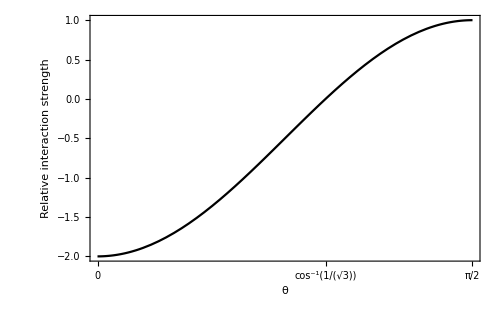

```mathematica
plt1=Plot[1-3 Cos[θ]^2,{θ,0,π/2},FrameLabel->{"θ","Relative interaction strength"},FrameTicks->{{Automatic,Automatic},{{0,ArcCos[1/(√3)],π/2},None}},GridLines->{{ArcCos[1/(√3)]}, {}}]
```

```mathematica
Export["/Users/gpatenotte/Documents/Research/Ni Group/cuaRetreatPoster/plt1.jpg",plt1,"jpg"]
```

/Users/gpatenotte/Documents/Research/Ni Group/cuaRetreatPoster/plt1.jpg

```mathematica
dataC={{71.354,0.12},{71.359,2}}
dataM={{71.354-0.003,0.12},{71.359+0.001,2}}
dataP={{71.354+0.003,0.12},{71.359-0.001,2}}
dataPP={{71.354+0.003,0.12},{71.359+0.001,2}}
dataMM={{71.354-0.003,0.12},{71.359-0.001,2}}
```

{{71.354,0.12},{71.359,2}}

{{71.351,0.12},{71.36,2}}

{{71.357,0.12},{71.358,2}}

{{71.357,0.12},{71.36,2}}

{{71.351,0.12},{71.358,2}}

```mathematica
((#[[2,1]]-x)/49.63 10^6/.Solve[Fit[#,{1,x},x]==0,x])&/@{dataC,dataM,dataP,dataMM,dataPP}
```

{{107.176},{192.917},{21.4352},{150.047},{64.3056}}

```mathematica
-1.51673+25.5749 .4
```

8.71323

```mathematica
3/8.71323
```

0.344304

```mathematica
(192.91694711101644+21.435216345795755)/2
```

107.176

```mathematica
192.91694711101644-107.1760817284061
```

85.7409

```mathematica
1 kHz/
```